Homework on Wolfram Mathematica 2

Arseniy Buchnev

10/27/2021

## Task 1

1) M=a_ij, i=1,2,3; j=1,2,3.
to calculate determinant, eigenvalues and eigenvectors for the matrix M, where a_ij is the random real numbers in the range (1, 5)

```mathematica
M = Table[RandomInteger[{1, 5}], {x, 3}, {y, 3}];
M // MatrixForm
```

M = Table[RandomInteger[{1, 5}], {x, 3}, {y, 3}];
M // MatrixForm

```mathematica
Det[M]
```

Det[M]

```mathematica
Eigenvalues[M] // N // TableForm
```

Eigenvalues[M] // N // TableForm

```mathematica
Eigenvectors[M] // N // TableForm
```

Eigenvectors[M] // N // TableForm

## Task 2

## 2) Plot all roots of the equation (∑_(n=0))^50 (-1)^n/(n!)x^n=0 on the complex plane

```mathematica
f[x_] := Block[{x}, ∑_(n=0)^50 (-1)^n/(n!)x^n == 0];
```

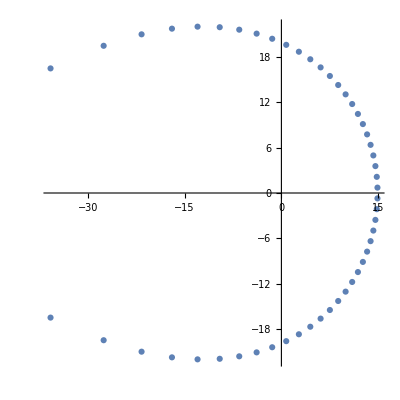

```mathematica
roots = x/.Solve[f[x], x] // N;
ListPlot[
Table[
{Re[roots][[i]], Im[roots][[i]]},
{i, 0, Length[roots]}],
AspectRatio->1]
```

## Task 3

3) Using ContourPlot[] and Manipulate[] to estimate R which corresponds to exactly 2 solution of the following system:
x^2+y^2=R^2
x y=1

## Solution

```mathematica
Block[{x, y, R},
Manipulate[ContourPlot[{x^2 + y^2 == R^2, x*y==1}, {x, -10, 10}, {y, -10, 10}], {R, 0, 3, 0.01}]]
```

R is approximately 1.4